```mathematica
SetDirectory[NotebookDirectory[]];
pathDrones=<<"pathDrones";
timeOrders=<<"timeOrders";
```

данные имеют следующую структуру:

pathDrones = {
				{drone 1 path},
				{drone 2 path},
				...,
				{drone 30 path}
			}, 
где drone i path имеет структуру:
			{
				{warehouse 1, order 1, time 1},
				{warehouse 2, order 2, time 2},
				...,
				{warehouse n, order n, time n},
			}, 
где warehouse i - склад, в который он предварительно залетал, order i - заказ, на который он после полетел и time i - время посещения i-го клиента

```mathematica
(*первые 10 клиентов дрона 1 и время их посещения, а также склад, куда залетал дрон*)
pathDrones⟦1,;;10⟧
```

{{1,778,8},{8,55,59},{5,902,102},{5,1137,196},{4,1216,273},{5,935,375},{6,152,443},{3,542,519},{5,967,604},{5,1104,667}}

timeOrders = {
			{times of order 1},
			...,
			{times of order 1250}
			},
где times of order j = {
					{droneID 1, time 1},
					...,
					{droneID n, time n}
				},
где droneID i - id дрона, который посетил j-ый заказ i-ым по счету в момент времени time i

```mathematica
timeOrders⟦1⟧(*посещения первого заказа*)
```

{{8,5996},{20,5895},{28,8135},{24,14545},{16,24420},{28,29815}}

я тут попытался построить из этого хотя бы первоначальный график без раскраски:

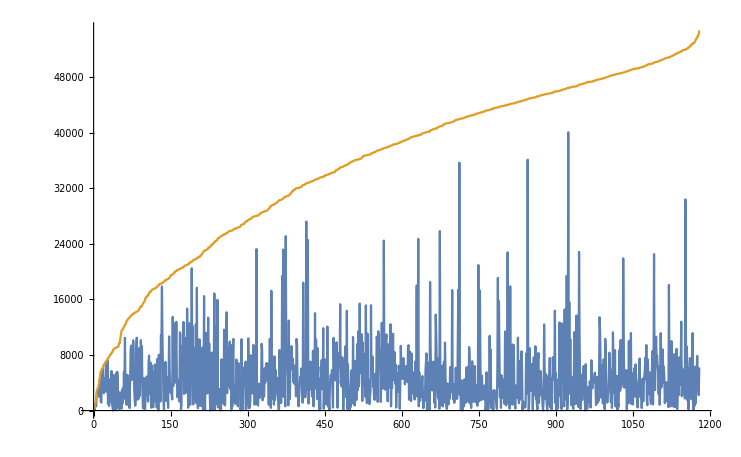

```mathematica
ListLinePlot[
Transpose[
SortBy[
Map[
Reverse,(*для удобства поменял в каждой паре время и номер дрона местами*)
{First@MinimalBy[#,Last],First@MaximalBy[#,Last]}&/@Select[timeOrders,Length@#>1&],(*беру min и max среди тех, которые доставляли хотя бы 2 дрона*)
{2}],
{Last,First}(*отсортировал пары по значению max*)
]
]⟦All,All,1⟧(*взял только значения времени, отбросил номера дронов*)
]
```

а потом я понял, что дронов у нас 30 штук, и если раскрасить нижний рукав, будет каша, поэтому решил попробовать сгруппировать исходные данные по номеру дрона и также отсортировать по max. получим 30 графиков:

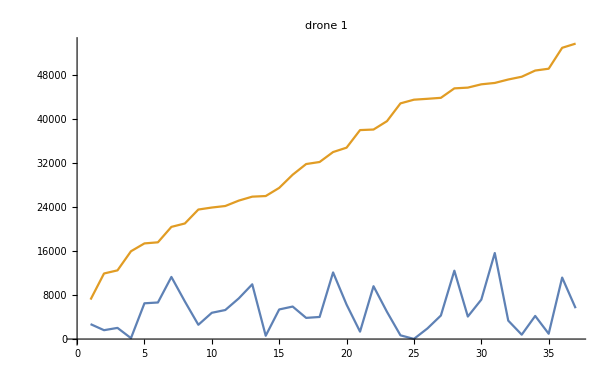
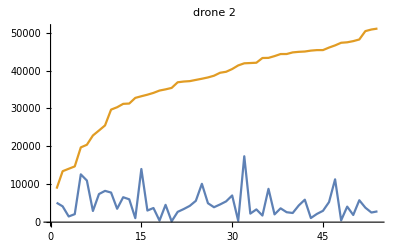
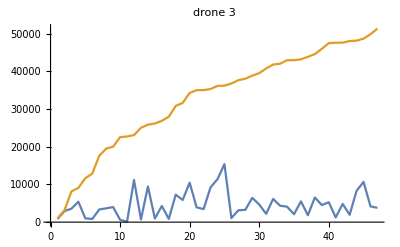
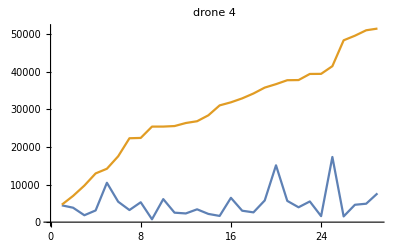
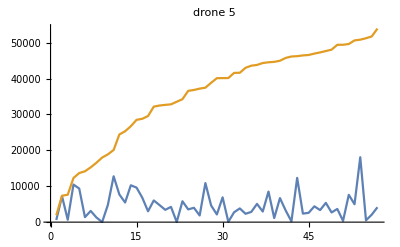
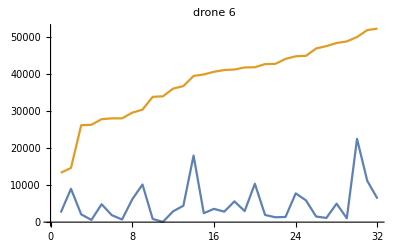
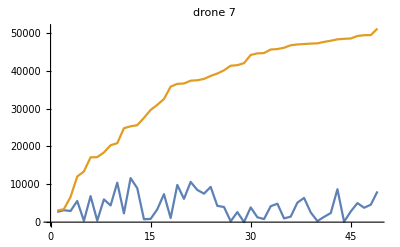
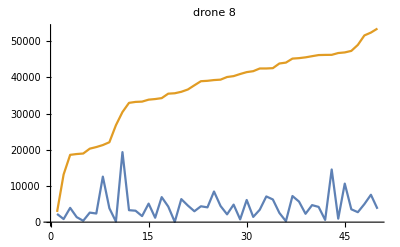

```mathematica
Table[
ListLinePlot[Transpose@
SortBy[
Normal@GroupBy[Map[Reverse,{First@MinimalBy[#,Last],First@MaximalBy[#,Last]}&/@Select[timeOrders,Length@#>1&],{2}],#⟦1,2⟧&]⟦i⟧,(*все то же самое, но сгруппировал по номеру дронов*)
{Last,First}
]⟦All,All,1⟧,
PlotLabel->"drone "<>ToString@i],
{i,30}]
```